# Integrals For Dummies

## If we can, you can!

Progetto d’esame: Matematica Computazionale & Calcolo Numerico e Software Didattico.

```mathematica
-Graphics--Graphics--Graphics--Graphics-
```

-Graphics- -Graphics- -Graphics- -Graphics-

Autori:

Tommaso Saracchini (email) | Domenico Coriale (email) | Giuseppe De Palma (email) | Eduart Uzeir (email)

Per iniziare ad usare questa applicazione ed imparare tutto ciò che serve sugli integrali, devi premere il pulsante START e seguire attentamente le istruzioni illustrate nella prossima slide. Buon divertimento!

Button[-Graphics-,SetDirectory[NotebookDirectory[]];<<"Package.m"; ButtonData→NotebookLocate["Index"];]

-Graphics-

# Indice

## Primo Livello:

Integrali Definiti

Integrali Indefiniti

## Secondo Livello:

Teorema Fondamentale

Metodi di Risoluzione degli Integrali

## Allenamento:

Esercizi su Integrali Definiti

Esercizi su Integrali Indefiniti

Esercizi Misti

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["FotoIniziale"]; ]Button[ImageResize[-Graphics-, 1000],ButtonData->NotebookLocate["DefiniteTheory"];]
```

-Graphics- -Graphics-

### Second level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

#### Third level section heading

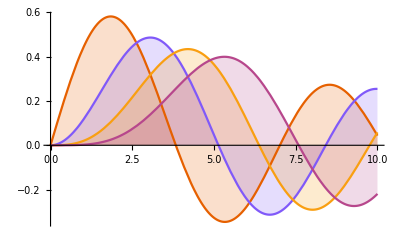

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

# Integrali Definiti

## Introduzione

Che cosa sono gli integrali definiti? E soprattutto: a cosa servono?
In Matematica, cosi` come in Fisica, puo` capitare di dover calcolare l’area che sta sotto ad una curva descritta da una funzione, gli integrali ci permettono di fare proprio questo.
Gli integrali sono lo strumento matematico che serve a calcolare l’area definita dalle curve delle funzioni.
Prendiamo una funzione, come ad esempio quella nell’immagine di sotto, e due punti “a” e “b” sull’asse delle “x” che sono gli estremi dell’intervallo al quale siamo interessati.
Ci chiediamo: come facciamo a calcolare l’area tra la curva , l’asse delle “x” e i due segmenti orizontali dati dalle equazioni delle rette x1=a e x2=b?
Per farlo ci servono gli integrali!

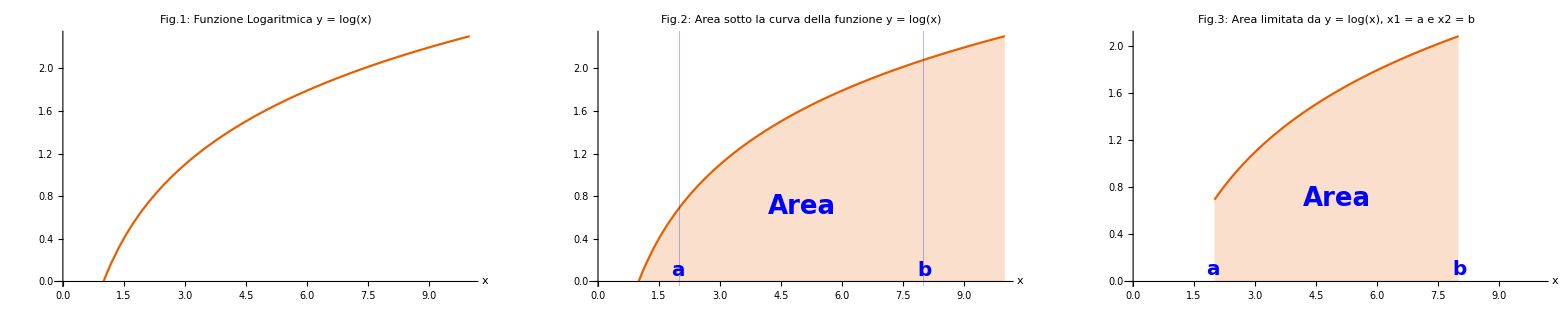

```mathematica
(* definisco i tre punti di rifferimento ossia sinistra, centro e desta*)
align[Right] = {1, 0};
align[Center] = {0, 0}; 
align[Left] = {-1, 0};
(* definisco lo stile del testo che voglio scrivere *)
lText = Text[Style["a", Blue, Bold, FontSize->20], {1.8, 0.1}, align[Left]];
cText = Text[Style["Area", Blue, Bold, Underlined, FontSize->26], {5.0, 0.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {8.2, 0.1}, align[Right]];

txt = Graphics[{lText, cText, rText}];
f[x_]:=Log[x]
(* costruisco i grafi in tre passi diversi *)
plot0=Plot[f[x], {x, 1, 10}, AxesOrigin->{0,0},PlotLabel->Style[Framed["Fig.1: Funzione Logaritmica y =" Log[x]], 22, Bold, Blue, Background->Lighter[Pink]], AxesLabel->Automatic];
plot0; (* la funzione logaritmica nel intervalo [0, 10]*)
plot1=Plot[f[x], {x, 1, 10}, AxesOrigin->{0,0}, Filling->Axis, PlotLabel->Style[Framed["Fig.2: Area sotto la curva della funzione y =" Log[x]], 22, Bold, Blue, Background->Lighter[Pink]], 
GridLines->{{{2, Blue}, {8, Blue}}, None}, PlotRange -> {{0, 10}, All}, AxesLabel->Automatic];
Show[plot1, txt];(* la funzione e i punti x=a e x=b *)
plot2=Plot[f[x], {x, 2, 8}, AxesOrigin->{0,0}, Filling->Axis, PlotLabel->Style[Framed["Fig.3: Area limitata da y = log(x), x1 = a e x2 = b"], 22, Bold, Blue, Background->Lighter[Pink]], 
(*GridLines->{{{2, Blue}, {8, Blue}}, None}*) PlotRange -> {{0, 10}, All}, AxesLabel->Automatic];
(* l'area che vogliamo calcolare *)
GraphicsRow[{plot0, Show[plot1, txt], Show[plot2,txt]}]
```

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["Index"]; ]Button[-Graphics-,ButtonData->NotebookLocate["Definite1"];]
```

-Graphics- -Graphics-

## Andiamo per passi...

Prendiamo una funzione semplice (la funzione costante): una retta che sia parallela all’asse delle “x” (ad esempio la retta di equazione y = 4).
Siamo interessati a calcolare nell’intervallo tra a = 1 e b = 3 come in figura, come facciamo?

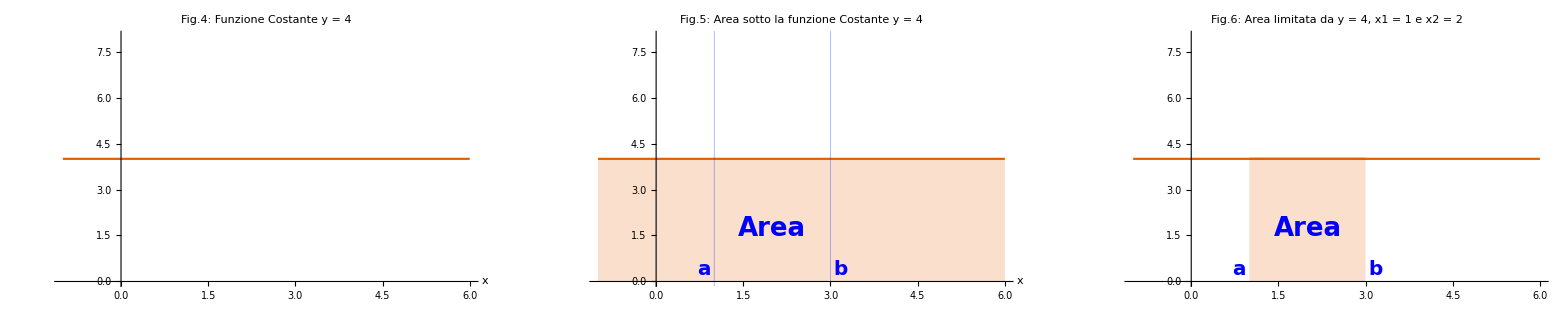

```mathematica
lText = Text[Style["a", Blue, Bold, FontSize->20], {0.7, 0.4}, align[Left]];
cText = Text[Style["Area", Blue, Bold, Underlined, FontSize->26], {2.0, 1.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {3.3, 0.4}, align[Right]];

txt2 = Graphics[{lText, cText, rText}];
funlim1 = -1;
funlim2 = 6;
f[x_]:=4
plot3=Plot[f[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.4: Funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic];
plot4=Plot[y=4, {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.5: Area sotto la funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], Filling->Axis, GridLines->{{{1, Blue}, {3, Blue}}, None},
AxesOrigin->{0,0}, AxesLabel->Automatic];
(*Plot[y=4, {x, 1, 3}, PlotLabel->Style[Framed["Fig.4: Funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], Filling->Axis, GridLines->{{{1, Blue}, {3, Blue}}, None}, 
AxesOrigin->{0,0}, AxesLabel->Automatic]*)
inlimit1 = 1;
inlimit2 = 3;
(*f[x_] = 100 - 8*x^2 + x^3;*)
g1 = Plot[f[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.6: Area limitata da y = 4, x1 = 1 e x2 = 2"], 22, Bold, Blue, Background->Lighter[Pink]]];
g2 = Plot[f[x], {x, inlimit1, inlimit2}, 
   Filling -> 0];
GraphicsRow[{plot3, Show[plot4, txt2], Show[g1, g2, txt2]}]
```

Semplice : E' un rettangolo!!! Sapendo che il Rettangolo dato ha base 2 ed altezza 4 l' area sara 8.
Quindi diciamo che l' INTEGRALE da 1 a 3 della funzione f (x) = 4 in dx e' uguale a 8! Facile no?! In simboli ∫_1^3 f(x)ⅆx = 8
Ti stai chiedendo cose’ dx? Lo scopriamo tra poco...! Intanto facciamo un altro semplice esempio.

```mathematica
Print[Framed["Informazioni supplementari sul" Hyperlink[RETTANGOLO, "http://mathworld.wolfram.com/Rectangle.html"]]]
```

Informazioni supplementari sul [RETTANGOLO](http://mathworld.wolfram.com/Rectangle.html)

```mathematica
Row[Button[-Graphics-,ButtonData->NotebookLocate["DefiniteTheory"]; ]Button[-Graphics-,ButtonData->NotebookLocate["Definite2"];]]
```

Row[-Graphics- -Graphics-]

## Andiamo per passi...

Prendiamo come funzione una qualunque retta inclinata, ad esempio f(x) = x + 1. 
Come facciamo a calcolare l’area nell’intervallo a = 1 e b = 4?
Questa volta abbiamo di fronte un Trapezio. Qui possiamo ancora arrangiarci con la geometria tradizionale.
Conoscendo la formula per calcolare l’area del Trapezio arriviamo a dire che:
																A=∫_1^5 f(x)ⅆx = 16

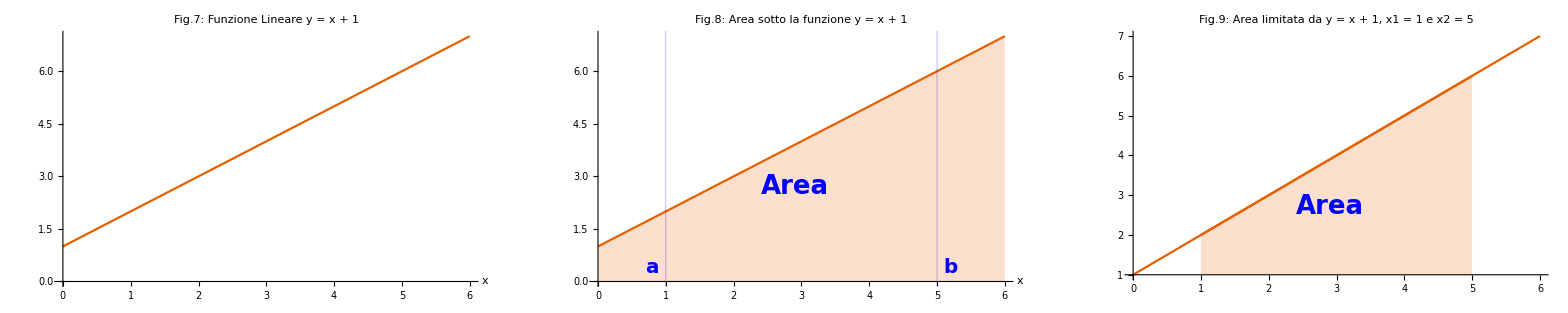

```mathematica
lText = Text[Style["a", Blue, Bold, FontSize->20], {0.7, 0.4}, align[Left]];
cText = Text[Style["Area", Blue, Bold, Underlined, FontSize->26], {2.9, 2.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {5.3, 0.4}, align[Right]];

txt2 = Graphics[{lText, cText, rText}];
funlim1 = 0;
funlim2 = 6;
f1[x_]:=x+1
plot3=Plot[f1[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.7: Funzione Lineare y = x + 1"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic];
plot4=Plot[f1[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.8: Area sotto la funzione y = x + 1"], 22, Bold, Blue, Background->Lighter[Pink]], Filling->Axis, GridLines->{{{1, Blue}, {5, Blue}}, None},
AxesOrigin->{0,0}, AxesLabel->Automatic];
(*Plot[y=4, {x, 1, 3}, PlotLabel->Style[Framed["Fig.4: Funzione Costante y = 4"], 22, Bold, Blue, Background->Lighter[Pink]], Filling->Axis, GridLines->{{{1, Blue}, {3, Blue}}, None}, 
AxesOrigin->{0,0}, AxesLabel->Automatic]*)
inlimit1 = 1;
inlimit2 = 5;
(*f[x_] = 100 - 8*x^2 + x^3;*)
g1 = Plot[f1[x], {x, funlim1, funlim2}, PlotLabel->Style[Framed["Fig.9: Area limitata da y = x + 1, x1 = 1 e x2 = 5"], 22, Bold, Blue, Background->Lighter[Pink]]];
g2 = Plot[f1[x], {x, inlimit1, inlimit2}, 
   Filling -> 1.0];
GraphicsRow[{plot3, Show[plot4, txt2], Show[g1, g2, txt2]}]
```

```mathematica
Print[Framed["Informazioni supplementari sul" Hyperlink[TRAPEZIO, "http://mathworld.wolfram.com/Trapezoid.html"]]]
```

Informazioni supplementari sul [TRAPEZIO](http://mathworld.wolfram.com/Trapezoid.html)

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["Definite1"]; ]Button[-Graphics-,ButtonData->NotebookLocate["Definite3"];]
```

-Graphics- -Graphics-

## Andiamo per passi...

Ma se volessimo calcolare l’area sotto delle funzioni curve, come questa per esempio f(x) =  ⅇ^x.oppure f(x) = x^3 -  8 x^2 + 100
In questo caso la geometria tradizionale non puo’ aiutarci ... per fortuna ci sono gli INTEGRALI DEFINIT.
Arriviamo quindi alla loro definizione:

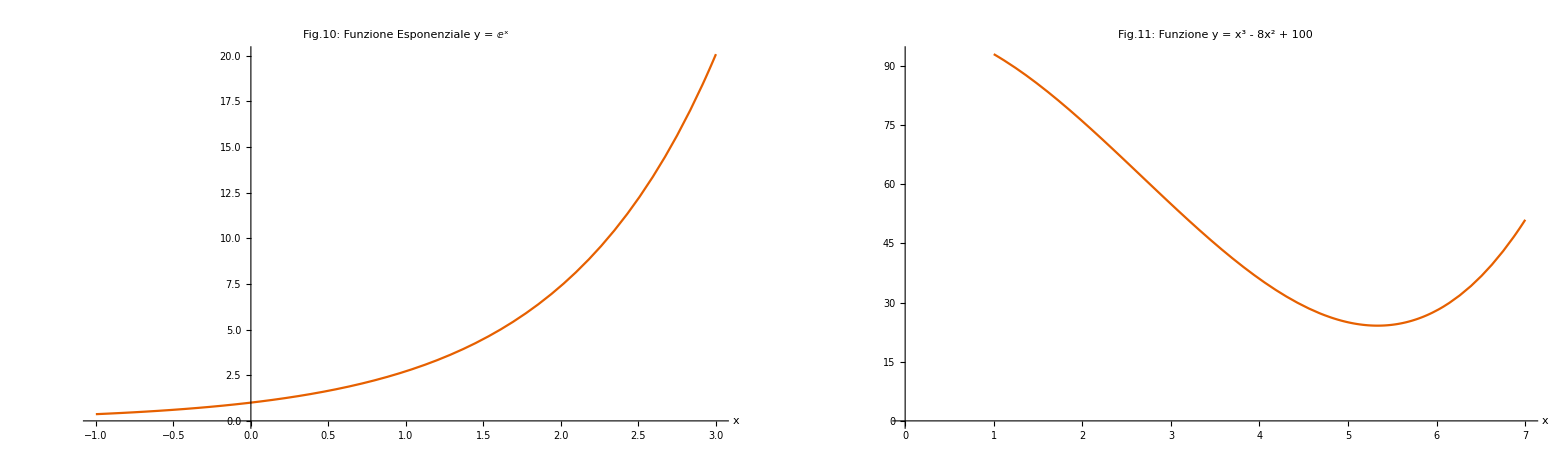

```mathematica
f2[x_]:= ⅇ^x;
f3[x_]:= 100-8*x^2+x^3;
funlim3 = -1;
funlim4 = 3;
funl1=1;
funl2=7;
plot5=Plot[f2[x], {x, funlim3, funlim4}, PlotLabel->Style[Framed["Fig.10: Funzione Esponenziale y = ⅇ^x"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic];
plot6=Plot[f3[x], {x, funl1, funl2}, PlotLabel->Style[Framed["Fig.11: Funzione y = x^3 - 8x^2 + 100"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic];

GraphicsRow[{plot5, plot6}]
```

Abbiamo incontrato nelle slide precedenti la scrittura ∫_a^b f(x)ⅆx, ma cosa vogliamo dire con questi simboli?
⟶ ∫  sta per “somma” di cosa? Lo vedremo tra pocco...
⟶ “a” e “b” sono gli estremi dell’intervallo di integrazione, cioe’ la base della figura 
⟶ f(x) e’ la funzione che conosciamo
⟶ dx rappresenta anche lui una” base”, ma qualle base?

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["Definite2"]; ]Button[-Graphics-,ButtonData->NotebookLocate["Definite4"];]
```

-Graphics- -Graphics-

## Definizioni

Possiamo pensare di dividere l’intervallo [a, b] in 4 intervalli uguali. Tracciamo dei segmenti verticali in modo da costruire dei rettangoli che non oltrepassano la funzione, come in figura.

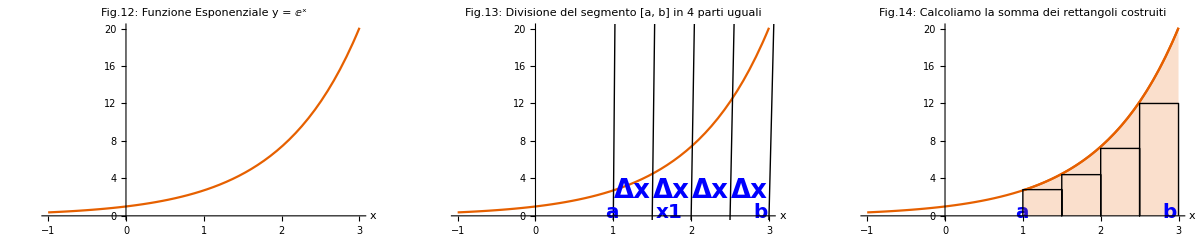

```mathematica
lText = Text[Style["a", Blue, Bold, FontSize->20], {0.9, 0.4}, align[Left]];
lTextt = Text[Style["x1", Blue, Bold, FontSize->20], {1.55, 0.4}, align[Left]];
cText = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {1.25, 2.7}, align[Center]];
cText2 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {1.75, 2.7}, align[Center]];
cText3 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {2.25, 2.7}, align[Center]];
cText4 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {2.75, 2.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {2.98, 0.4}, align[Right]];

lText1 = Text[Style["a", Blue, Bold, FontSize->20], {0.9, 0.4}, align[Left]];
cText1 = Text[Style["", Blue, Bold, Underlined, FontSize->26], {2.9, 2.7}, align[Center]];
rText1 = Text[Style["b", Blue, Bold, FontSize->20], {2.97, 0.4}, align[Right]];

txt3 = Graphics[{lText,lTextt, cText, cText2,cText3,cText4, rText}];

txt4 = Graphics[{lText1, cText1, rText1}];

plott=Plot[f2[x], {x, -1, 3}, PlotLabel->Style[Framed["Fig.12: Funzione Esponenziale y = ⅇ^x"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic]; (**)
plott0=Plot[f2[x], {x, -1, 3}, PlotLabel->Style[Framed["Fig.13: Divisione del segmento [a, b] in 4 parti uguali"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic,
Epilog->{
InfiniteLine[{1, 0}, {1, 1000}], 
InfiniteLine[{1.5, 0}, {1.5, 1000}],
InfiniteLine[{2, 0}, {2, 1000}],
InfiniteLine[{2.5, 0}, {2.5, 1000}],
InfiniteLine[{3, 0}, {3, 1000}]}];
plott1=Plot[f2[x], {x, -1, 3}, PlotLabel->Style[Framed["Fig.14: Calcoliamo la somma dei rettangoli costruiti"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic,
Epilog->{Line[{{1, 0}, {1, 2.8}, {1.5, 2.8}, {1.5, 0}, {1.5, 4.4}, {2, 4.4}, {2, 0}, {2, 7.2}, {2.5, 7.2}, {2.5, 0}, {2.5, 12}, {3, 12}, {3, 0}}]}];
g2 = Plot[f2[x], {x, 1, 3}, 
   Filling -> 0];
GraphicsRow[{plott,Show[plott0, txt3], Show[plott1, g2, txt4]}]
```

Abbiamo quindi quatro rettangolicon la stessa base Δx, ognuno con altezza diversa, ad esempio il primo ha altezza f(a), il secondo f(x1) e cosi via ... fino all’ultimo f(b).
Chiamo S4 la soma delle aree dei quatro rettangoli che ne sono usciti.
Osserviamo che se sommiamo le aree di questi 4 rettangoli otteniamo un’area minore dell’area A sottesa alla curva (indicata con il color rosa in figura 14) , 
cioe’ abbiamo che S4 < A. 
Possiamo fare meglio?!

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["Definite3"]; ]Button[-Graphics-,ButtonData->NotebookLocate["Definite5"];]
```

-Graphics- -Graphics-

## Definizioni

Come possiamo ridurre l’errore tra la misura dell’area che abbiamo calcolato e la misura dell’area “vera”?
Possiamo dividere ulteriormente l’intervallo! Ad esempio in 10 intervalli uguali.

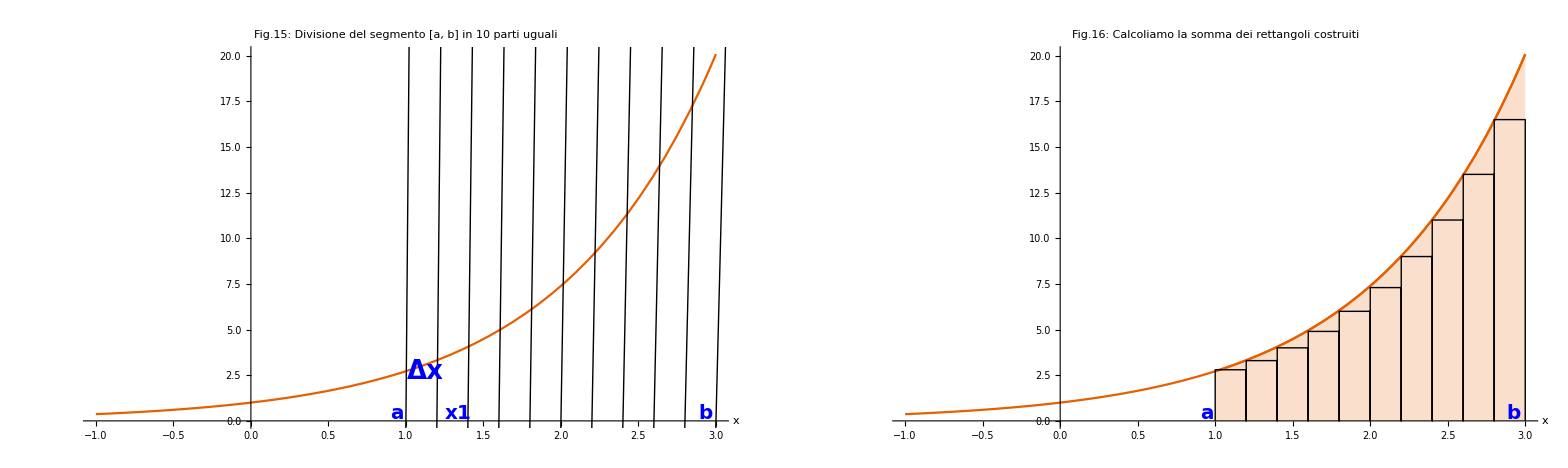

```mathematica
lText = Text[Style["a", Blue, Bold, FontSize->20], {0.9, 0.4}, align[Left]];
lTextt = Text[Style["x1", Blue, Bold, FontSize->20], {1.55, 0.4}, align[Left]];
lTexttA = Text[Style["x1", Blue, Bold, FontSize->20], {1.25, 0.4}, align[Left]];
cText = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {1.25, 2.7}, align[Center]];
cTextA = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {1.125, 2.7}, align[Center]];
cText2 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {1.75, 2.7}, align[Center]];
cText3 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {2.25, 2.7}, align[Center]];
cText4 = Text[Style["Δx", Blue, Bold, Underlined, FontSize->26], {2.75, 2.7}, align[Center]];
rText = Text[Style["b", Blue, Bold, FontSize->20], {2.98, 0.4}, align[Right]];

lText1 = Text[Style["a", Blue, Bold, FontSize->20], {0.9, 0.4}, align[Left]];
cText1 = Text[Style["", Blue, Bold, Underlined, FontSize->26], {2.9, 2.7}, align[Center]];
rText1 = Text[Style["b", Blue, Bold, FontSize->20], {2.97, 0.4}, align[Right]];

txt3 = Graphics[{lText, lTexttA, cTextA, rText}];

txt4 = Graphics[{lText1, cText1, rText1}];
plott0=Plot[f2[x], {x, -1, 3}, PlotLabel->Style[Framed["Fig.15: Divisione del segmento [a, b] in 10 parti uguali"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic,
Epilog->{
InfiniteLine[{1, 0}, {1, 1000}],
InfiniteLine[{1.2, 0}, {1.2, 1000}], 
InfiniteLine[{1.4, 0}, {1.4, 1000}],
InfiniteLine[{1.6, 0}, {1.6, 1000}],
InfiniteLine[{1.8, 0}, {1.8, 1000}],
InfiniteLine[{2, 0}, {2, 1000}],
InfiniteLine[{2.2, 0}, {2.2, 1000}],
InfiniteLine[{2.4, 0}, {2.4, 1000}],
InfiniteLine[{2.6, 0}, {2.6, 1000}],
InfiniteLine[{2.8, 0}, {2.8, 1000}],
InfiniteLine[{3, 0}, {3, 1000}]}];
plott1=Plot[f2[x], {x, -1, 3}, PlotLabel->Style[Framed["Fig.16: Calcoliamo la somma dei rettangoli costruiti"], 22, Bold, Blue, Background->Lighter[Pink]], AxesOrigin->{0,0}, AxesLabel->Automatic,
Epilog->{Line[{{1, 0}, {1, 2.8}, {1.2, 2.8}, {1.2, 0}, {1.2, 3.3}, {1.4, 3.3}, {1.4, 0}, {1.4, 4}, {1.6, 4}, {1.6, 0}, {1.6, 4.9}, {1.8, 4.9}, {1.8, 0}, {1.8, 6}, {2, 6}, {2, 0}, 
{2, 7.3}, {2.2, 7.3}, {2.2, 0}, {2.2, 9}, {2.4, 9}, {2.4, 0}, {2.4, 11}, {2.6, 11}, {2.6, 0}, {2.6, 13.5}, {2.8, 13.5}, {2.8, 0}, {2.8, 16.5}, {3, 16.5}, {3, 0}}]}];
g2 = Plot[f2[x], {x, 1, 3}, 
   Filling -> 0];
GraphicsRow[{Show[plott0, txt3], Show[plott1, g2, txt4]}]
```

Abbiamo pero’ lo stesso problema, possiamo notare dalla figura che la soma dell’area nei 10 rettangoli, cioe’ S10 e’ ancora minore dell’area A sottesa alla curva.

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["Definite4"]; ]Button[-Graphics-,ButtonData->NotebookLocate["Definite6"];]
```

-Graphics- -Graphics-

## Definizioni

In generale se dividessimo l’intervallo [a, b] in N intervalli avremo che la somma delle aree degli N rettangoli, sara’ sempre minore dell’area che vogliamo calcolare, 
cioe’ SN < A per ogni N numero di intervalli.
Osserviamo dalla figura che, al crescere di N, i rettangoli diventano sempre piu’ piccoli e la differenza tra SN e A e’ sempre minore.
Prendiamo per esempio la funzione f(x) = 3x^2 + 5.

```mathematica
f[x_]:= 3x^2+5
plotChart[nrettangoli_] := Module[{}, low = 0; high = 2;
delta = (high - low)/nrettangoli;
colsum = Graphics[{FaceForm[{Opacity[0.7]}], Table[{Hue[1, 0.6, 0.8], EdgeForm[Thin], Rectangle[{low + n * delta, 0}, {low + (n + 1) * delta, f[low + n * delta]}]}, {n, 1, nrettangoli}]}, ImageSize->500, AspectRatio->1];
curve=Plot[f[x], {x, low, high}, PlotStyle->Thick, ImageSize->60];];
Manipulate[-Graphics--Graphics-]
```

Non ci resta altro da fare che “mandare N all’infinito”, e cioe’ calcolare: lim_(N→∞) SN. Il risultato che ne saltera’ fuori sara’ proprio l’Area che savamo cercando!
Quindi,  ricapitoliamo: L’Area che vogliamo calcolare e’:
 La somma ∫ nell’intervallo [a, b] di “infiniti rettangoli” di base “infinitamente piccola”, dx e altezza f(x)     ∫_a^b f(x)ⅆx

```mathematica
Print[Framed["Informazioni supplementari sui" Hyperlink[LIMITI, "http://mathworld.wolfram.com/Limit.html"]]]
```

Informazioni supplementari sui [LIMITI](http://mathworld.wolfram.com/Limit.html)

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["Definite5"]; ]Button[ImageResize[-Graphics-, 1000],ButtonData->NotebookLocate["IndefiniteTheory"];]
```

-Graphics- -Graphics-

# Integrali Indefiniti

## Introduzione

Prima di spiegare che cosa e’ l’integrale indefinito, dobbiamo fare qualche premessa.
Partiamo dalla definizione di “primitiva di una funzione”: 
Sia f:[a, b]→ℜ, una funzione continua. Una funzione F(x) derivabile nell’intervallo [a, b] e’ una primitiva o antiderivata della funzione f se: F’(x) = f(x) per ogni x in [a, b]
In altre parole una primitivaa di una funzione f(x) non e’ altro che una funzione che una volta derivata dia proprio f.
Esempio 1:

Se f(x) = 2x, allora una sua primitiva e’ F(x) = x^2 proprio perche’ la derivata di x^2 e’ 2x. D[ x^2 ] = 2x
Esempio 2:

Se f(x) = cos(x), allora una sua primitiva e’ F(x) = sin(x) perche’ la derivata di sin(x) e’ cos(x). D[ cos(x) ] = sin(x)

```mathematica
Print[Framed["Informazioni supplementari sui" Hyperlink[DERIVATI, "http://mathworld.wolfram.com/Derivative.html"]]]
```

Informazioni supplementari sui [DERIVATI](http://mathworld.wolfram.com/Derivative.html)

```mathematica
Button[ImageResize[-Graphics-, 1000],ButtonData->NotebookLocate["DefiniteTheory"]; ]Button[-Graphics-,ButtonData->NotebookLocate["Indefinite1"];]
```

-Graphics- -Graphics-

## Introduzione

Possiamo fare un osservazione:
Avete notato che nella definizione c’e’ scritto “e’ una primitiva” e non “la primitiva”?
Riprendendo la funzione f(x) = 2x, possiamo osservare che anche F(x)=x^2 + 1 e’ anch’essa una primitiva di f, infatti D[ x^2+1 ] = 2x.
Abbiamo trovato due primitive di una stessa funzione! Ma quante ce ne saranno?
Basti pensare che, tornando all’esempio precedente, potevamo aggiungere alla primitiva F(x) una costante qualsiasi dato che la derivata di una costante vale zero.
Infatti possiamo scrivere:  D[ x^2 + a ] = D[ x^2] + D[ a ] = 2x.

Percio’ vediamo che se una funzione f(x) ammette primitiva F(x), allora ne ha INFINITE che differiscono tutte da F(x) di una costante additiva ( c ).

A questo punto sapendo che una funzione ammette una primitiva, ne ammette infinite. Ha quindi senso definire “l’insime di tutte le primitive” di una funzione e di attribuirgli
un nome: lo chiameremo INTEGRALE INDEFINITO DI UNA FUNZIONE.

Definizione:

Sia f una funzione, si chiama INTEGRALE INDEFINITO di f l’insieme di tutte le primitive della funzione f e si indica con il simbolo: ∫f(x)ⅆx.

In base a quanto detto sulle primitive possiamo dire che: ∫f(x)ⅆx = F(x) + c dove F(x) e’ una primitiva di f.

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["IndefiniteTheory"]; ]Button[-Graphics-,ButtonData->NotebookLocate["Indefinite2"];]
```

-Graphics- -Graphics-

## Introduzione

Anche se la notazione non lo lascia intendere esplicitamente sottolineiamo che l’integrale indefinito identifica un insieme di funzioni e non una funzione in particolare.
Questo fatto viene messo in evidenza dalla costante additiva “c”, che’ arbitraria e non deve essere omessa.
Facciamo qualche semplice esempio per chiarire le idee:

1. ∫x ⅆx = x^2/2 + c 		2. ∫e^x ⅆx = e^x + c		3. ∫1/x ⅆx=log(x)+c		4. ∫1/x^2 ⅆx= - 1/x+c		5.∫x^2 ⅆx=x^3/3 + c

per “c” costante qualsiasi.

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["Indefinite1"]; ]Button[-Graphics-,ButtonData->NotebookLocate["FundTheorem"];]
```

-Graphics- -Graphics-

# Teorema Fondamentale

## Introduzione

Quello che vediamo ora e’ che la notazione utilizzata per gli integrali definiti e indefiniti e’ molto simile ... perche’? Le definizioni che abbiamo dato ad entrambe sono completamente diverse.
L’integrale definito di una funzione in un certo intervallo indica un’area e cioe’ un numero.
L’integrale indefinito di una funzione e’ invece un insieme di funzioni, che non ha nulla a che vedere con il concetto di area.
Ma allora perche’ le loro notazioni sono cosi simili? La risposta la troviamo nel seguente teorema.

## Teorema fondamentale del calcolo integrale

Sia f:[a, b]→ℝ una funzione e sia G(x) una sua primitiva. Allora ∫_a^b f(x)ⅆx=G(b)-G(a).

Questo teorema fondamentale stabilisce un legame tra l’integrale definito e l’integrale indefinito, il quale non era per niente ovvio dalle sole definizioni date ad entrambi!
In particolare, ci permette di risolvere integrali definiti usando il concetto di primitiva di una funzione, e cioe’ con gli integrali indefiniti.
Ecco svelato il perche’ delle notazioni molto simili, ma andiamo subito a calcolare il nostro primo integrale.

```mathematica
Print[Framed["Informazioni supplementari sul" Hyperlink[TEOREMA FONDAMENTALE DEL CALCOLO INTEGRALE, "http://mathworld.wolfram.com/FundamentalTheoremsofCalculus.html"]]]
```

Informazioni supplementari sul [CALCOLO DEL FONDAMENTALE INTEGRALE TEOREMA](http://mathworld.wolfram.com/FundamentalTheoremsofCalculus.html)

```mathematica
Button[ImageResize[-Graphics-, 1000],ButtonData->NotebookLocate["IndefiniteTheory"]; ]Button[-Graphics-,ButtonData->NotebookLocate["FundTheorem1"];]
```

-Graphics- -Graphics-

## Il mio primo integrale

Vogliamo calcolare l’area sottesa alla curva di funzione f(x)=x^2 nell’intervallo [1, 2]

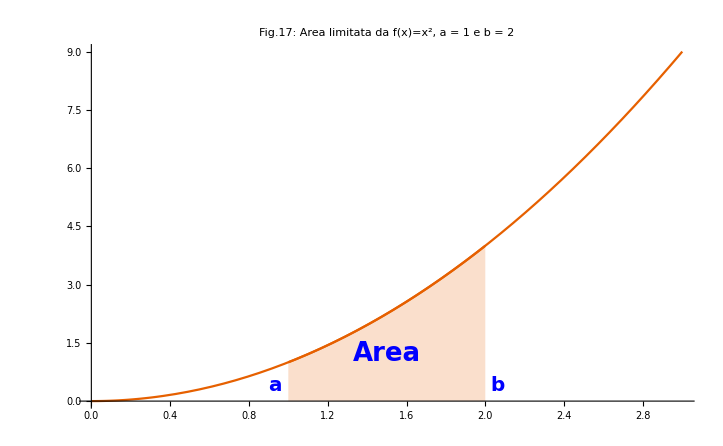

```mathematica
leftText = Text[Style["a", Blue, Bold, FontSize->20], {0.9, 0.4}, align[Left]];
centerText = Text[Style["Area", Blue, Bold, FontSize->26], {1.5, 1.2}, align[Center]];
rightText = Text[Style["b", Blue, Bold, FontSize->20], {2.1, 0.4}, align[Right]];
txt5 = Graphics[{leftText, centerText, rightText}];

fu[x_]:=x^2;
go1 = Plot[fu[x], {x, 0, 3}, PlotLabel->Style[Framed["Fig.17: Area limitata da f(x)=x^2, a = 1 e b = 2"], 22, Bold, Blue, Background->Lighter[Pink]]];
go2 = Plot[fu[x], {x, 1, 2}, 
   Filling -> 0];
Show[go1, go2, txt5]
```

Quindi possiamo calcolare l’area A con la seguente formula: A =∫_0^1 x^2 ⅆx.
Il teorema precedente mi dice che devo trovare una primitiva della funzione f(x) = x^2.
Ricordandosi le regole di derivazione dei polinomi, non dovrebe risultare difficile trovare: G(x) =x^3/3
Trucco:

Notate che, mi basta conoscere una sola primitiva di f(x), e quindi per semplicita’ posso prendere la primitiva con la costante c = 0!
Una volta trovata G(x) vado ad applicare il teorema:
												A = ∫_1^2 x^2 ⅆx = G(2) - G(1) = 2^3/3-1^3/3= 8/3 - 1/3 = 7/3

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["FundTheorem"]; ]Button[-Graphics-,ButtonData->NotebookLocate["FundTheorem2"];]
```

-Graphics- -Graphics-

## Il mio primo integrale

Osservate che se avessimo preso una qualunque altra primitiva G(x) = x^3/3 + c, con c un numero qualsiasi, avremmo avuto lo stesso risultato.

											A =∫_1^2 x^2 ⅆx=G(2)-G(1)=(2^3/3+c)-(1^3/3+c)=8/3-1/3=7/3
											
Questo perche, in questo procedimento, le costanti si eliminano a vicenda.

Vediamo un’altro esempio.
Calcolare l’area sotto alla funzione coseno tra - π/2 e π/2.

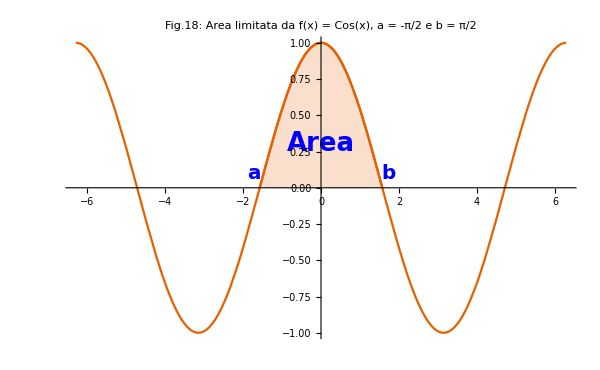

```mathematica
leftText1 = Text[Style["a", Blue, Bold, FontSize->20], {- 1.9, 0.1}, align[Left]];
centerText1 = Text[Style["Area", Blue, Bold, FontSize->26], {0, 0.3}, align[Center]];
rightText1 = Text[Style["b", Blue, Bold, FontSize->20], {1.9, 0.1}, align[Right]];
txt6 = Graphics[{leftText1, centerText1, rightText1}];

fu1[x_]:=Cos[x];
go11 = Plot[fu1[x], {x, -2π, 2π}, PlotLabel->Style[Framed["Fig.18: Area limitata da f(x) = Cos(x), a = -π/2 e b = π/2"], 22, Bold, Blue, Background->Lighter[Pink]]];
go22 = Plot[fu1[x], {x, -π/2, π/2}, 
   Filling -> 0];
   Show[go11, go22, txt6]
```

L’area sara’ data dalla formula,	 A = ∫_(-π/2)^(π/2) cos(x) ⅆx
Troviamo una primitiva, G(x)=sin(x), la prendiamo con costante c = 0 per l’osservazione precedente e abbiamo:

										A =∫_(-π/2)^(π/2) cos(x)ⅆx=G(π/2)-G(-π/2)=sin(π/2)-sin(-π/2)=1-(-1)=2

```mathematica
Print[Framed["Informazioni supplementari sulle" Hyperlink[FUNZIONI TRIGONOMETRICHE, "http://mathworld.wolfram.com/TrigonometricFunctions.html"]]]
```

Informazioni supplementari sulle [FUNZIONI TRIGONOMETRICHE](http://mathworld.wolfram.com/TrigonometricFunctions.html)

```mathematica
Button[-Graphics-,ButtonData->NotebookLocate["FundTheorem1"]; ]
```

-Graphics-

## Slide

This is a text cell.